# Introduction to (Geometric) Clifford Algebras: Applications to classical and quantum relativistic mechanics

## By Renan Cabrera

### Routines

```mathematica
<<Notation`
```

```mathematica
Notation[x_^— ⟺ CliffordConjugationSL2C[x_]]
```

```mathematica
Notation[x_^* ⟺ Conjugate[x_]]
```

```mathematica
Notation[x_^† ⟺ ConjugateTranspose[x_]]
```

```mathematica
Notation[Subscript[σ, i_] ⟺ PauliMatrix[i_]]
```

```mathematica
Notation[∂x_ ⟺ paraGradient[x_]]
```

```mathematica
Notation[∂^— x_ ⟺ paraGradientBar[x_]]
```

```mathematica
CliffordConjugationSL2C[({{L11_, L12_}, {L21_, L22_}})]:= ({{L22, -L12}, {-L21, L11}})
```

```mathematica
Symbolize[u^_]
```

```mathematica
Symbolize[Subscript[u, _]]
```

```mathematica
Symbolize[x^_]
```

```mathematica
Symbolize[Subscript[x, _]]
```

```mathematica
Symbolize[y^_]
```

```mathematica
Symbolize[Subscript[y, _]]
```

```mathematica
Symbolize[A^_]
```

```mathematica
Symbolize[Subscript[A, _]]
```

```mathematica
Symbolize[Subscript[𝔹, _]]
```

```mathematica
Symbolize[Subscript[𝔼, _]]
```

```mathematica
Symbolize[Subscript[ψ, _]]
```

```mathematica
Notation[Subscript[⟨x_⟩, "H"] ⟺ HermitianPart[x_]]
```

```mathematica
Notation[Subscript[⟨x_⟩, "A"] ⟺ AntiHermitianPart[x_]]
```

```mathematica
Notation[Subscript[⟨x_⟩, "V"] ⟺ VectorPart[x_]]
```

```mathematica
Notation[Subscript[⟨x_⟩, "S"] ⟺ ScalarPart[x_]]
```

```mathematica
ForceConjugateTranspose[x_]:= Transpose[x]/.Complex[a_,b_]:> Complex[a,-b]
```

```mathematica
ForceConjugate[x_]:= x/.Complex[a_,b_]:> Complex[a,-b]
```

```mathematica
RealPart[x_]:= (x+ Conjugate[x])/2
```

```mathematica
ImaginaryPart[x_]:= (x- Conjugate[x])/2
```

```mathematica
DerivativeFormat[w_]:=Block[{},
w/.{Derivative[1,0,0,0][f_][x__]:> HoldForm[D[f, 0]],Derivative[0,1,0,0][f_][x__]:> HoldForm[D[f, 1]],
Derivative[0,0,1,0][f_][x__]:> HoldForm[D[f, 2]],
Derivative[0,0,0,1][f_][x__]:> HoldForm[D[f, 3]]}
]
```

```mathematica
CompactFormat[w_]:=Block[{},
w//.{Derivative[1,0,0,0][f_][x__]:> HoldForm[D[f, 0]],Derivative[0,1,0,0][f_][x__]:> HoldForm[D[f, 1]],
Derivative[0,0,1,0][f_][x__]:> HoldForm[D[f, 2]],
Derivative[0,0,0,1][f_][x__]:> HoldForm[D[f, 3]],
f_?AtomQ[x0_?AtomQ,x1_?AtomQ,x2_?AtomQ,x3_?AtomQ]/;f=!=Times:> f}
]
```

## Algebra of the Physical Space (APS)

The algebra of physical space introduced by W. Baylis  (See Refs. [1, 2, 3]) is an elegant algebraic formalism that can be regarded as an extension of the standard vector calculus to deal with the Minkowski space. These lectures slightly depart from the axiomatic approach in the literature by extensively using the Pauli matrix representation. In this way, we lose some mathematical elegance but I hope I provide a more familiar environment constructed on top of standard linear algebra.

There is a second set of lectures treating the Space-Time algebra (STA) developed by Hestenes.

These lectures are written in Mathematica including a description of the formalism and the implementation of routines to perform symbolic and numerical calculations. This gives the student the ability to further explore beyond the provided examples and pursue a deeper understanding of the topic. It is like having a live document that is capable to provide answers on the fly.

These lectures are written in Mathematica 11.1 and can be alternatively opened by the free Mathematica CDF reader available in https://www.wolfram.com/cdf-player/.

## Basics

```mathematica
Grid[
{
{Style["Scalar",FontFamily->"TeX Gyre Pagella"],  Grid[{{HoldForm[Subscript[σ, 0]] ,"=",MatrixForm[ Subscript[σ, 0] ]}}] }
,
{Style["Vector",FontFamily->"TeX Gyre Pagella"],    Grid[{{HoldForm[Subscript[σ, 1]],"=",MatrixForm@Subscript[σ, 1]},{HoldForm[Subscript[σ, 2]],"=",MatrixForm@Subscript[σ, 2]},{HoldForm[Subscript[σ, 3]],"=",MatrixForm@Subscript[σ, 3]}}]  }
,
{Style["Bivector",FontFamily->"TeX Gyre Pagella"], Grid[
{{HoldForm[Subscript[σ, 1] Subscript[σ, 2]],"=",HoldForm[ ⅈ Subscript[σ, 3]],"=",MatrixForm[Subscript[σ, 1].Subscript[σ, 2]]},{HoldForm[Subscript[σ, 2] Subscript[σ, 3]],"=",HoldForm[ ⅈ Subscript[σ, 1]],"=",MatrixForm[Subscript[σ, 2].Subscript[σ, 3]]},{HoldForm[Subscript[σ, 3] Subscript[σ, 1]],"=",HoldForm[ ⅈ Subscript[σ, 2]],"=",MatrixForm[Subscript[σ, 3].Subscript[σ, 1]]}}] },
{Style["PseudoScalar",FontFamily->"TeX Gyre Pagella"],Grid[{{HoldForm[Subscript[σ, 123]],"=",HoldForm[Subscript[σ, 1] Subscript[σ, 2] Subscript[σ, 3]],"=",MatrixForm[Subscript[σ, 1].Subscript[σ, 2].Subscript[σ, 3]]}}]}
}
,Frame->All]
```

Scalar | σ_0 | = | (1 | 0
0 | 1)
Vector | σ_1 | = | (0 | 1
1 | 0)
σ_2 | = | (0 | -ⅈ
ⅈ | 0)
σ_3 | = | (1 | 0
0 | -1)
Bivector | σ_1 σ_2 | = | ⅈ σ_3 | = | (ⅈ | 0
0 | -ⅈ)
σ_2 σ_3 | = | ⅈ σ_1 | = | (0 | ⅈ
ⅈ | 0)
σ_3 σ_1 | = | ⅈ σ_2 | = | (0 | 1
-1 | 0)
PseudoScalar | σ_123 | = | σ_1 σ_2 σ_3 | = | (ⅈ | 0
0 | ⅈ)

### Conjugations

```mathematica
Column[{Style["Hermitian Conjugation",FontFamily->"MathJax_Caligraphic"],
Grid[ 
{{"Hermitian",Grid[{{HoldForm[SuperDagger[Subscript[σ, 0]]] ,"=",HoldForm[Subscript[σ, 0]]},{HoldForm[SuperDagger[Subscript[σ, k]]] ,"=",HoldForm[Subscript[σ, k]]}}]},
{"AntiHermitian",Grid[{{HoldForm[SuperDagger[Subscript[σ, jk]]] ,"=",HoldForm[-Subscript[σ, jk]]},{HoldForm[SuperDagger[Subscript[σ, 123]]] ,"=",HoldForm[-Subscript[σ, 123]]}}]}
} 
,Frame->All,Spacings->{2.5, 1}]
},Frame->False,Background->White]
```

Hermitian Conjugation
Hermitian | σ_0^† | = | σ_0
σ_k^† | = | σ_k
AntiHermitian | σ_jk^† | = | -σ_jk
σ_123^† | = | -σ_123

```mathematica
Column[{Style["Clifford Conjugation",FontFamily->"MathJax_Caligraphic"],
Grid[ 
{{"Scalar",Grid[{{ HoldForm[Subscript[σ, 0]^—],"=",HoldForm[Subscript[σ, 0]]},{HoldForm[HoldForm[Subscript[σ, 123]^—]] ,"=",HoldForm[Subscript[σ, 123]]}}]},
{"Vector",Grid[{{HoldForm[Subscript[σ, k]^—] ,"=",HoldForm[-Subscript[σ, k]]},{HoldForm[HoldForm[Subscript[σ, jk]^—]] ,"=",HoldForm[-Subscript[σ, jk]]}}]}
} 
,Frame->All,Spacings->{5, 1}]
},Frame->False]
```

Clifford Conjugation
Scalar | σ_0^— | = | σ_0
σ_123^— | = | σ_123
Vector | σ_k^— | = | -σ_k
σ_jk^— | = | -σ_jk

### Extracting Scalar Part

```mathematica
CliffordConjugationSL2C[ ({{Subscript[a, 11], Subscript[a, 12]}, {Subscript[a, 21], Subscript[a, 22]}}) ]//MatrixForm
```

(a_22 | -a_12
-a_21 | a_11)

```mathematica
ScalarPart[x_]:=(x+CliffordConjugationSL2C[x])/2
```

```mathematica
VectorPart[x_]:=(x-CliffordConjugationSL2C[x])/2
```

```mathematica
ScalarPart[ a Subscript[σ, 0] + b Subscript[σ, 1]]//MatrixForm
```

(a | 0
0 | a)

```mathematica
VectorPart[ a Subscript[σ, 0] + b Subscript[σ, 1]]//MatrixForm
```

(0 | b
b | 0)

#### Note 1 : The trace almost reproduces the role of the scalar part

```mathematica
1/2 Tr[a Subscript[σ, 0] + b Subscript[σ, 1]] Subscript[σ, 0]//MatrixForm
```

(a | 0
0 | a)

#### Note 2 : The Clifford conjugation can be used to calculate the determinant

```mathematica
Det@({{Subscript[a, 11], Subscript[a, 12]}, {Subscript[a, 21], Subscript[a, 22]}})
```

-a_12 a_21+a_11 a_22

```mathematica
1/2Tr[ ({{Subscript[a, 11], Subscript[a, 12]}, {Subscript[a, 21], Subscript[a, 22]}}).CliffordConjugationSL2C[({{Subscript[a, 11], Subscript[a, 12]}, {Subscript[a, 21], Subscript[a, 22]}})] ]//Expand
```

-a_12 a_21+a_11 a_22

#### Note 3 : The Clifford conjugation is the product of the inverse with the determinant

```mathematica
CliffordConjugationSL2C[({{Subscript[a, 11], Subscript[a, 12]}, {Subscript[a, 21], Subscript[a, 22]}})]//MatrixForm
```

(a_22 | -a_12
-a_21 | a_11)

```mathematica
Det[({{Subscript[a, 11], Subscript[a, 12]}, {Subscript[a, 21], Subscript[a, 22]}})]Inverse[({{Subscript[a, 11], Subscript[a, 12]}, {Subscript[a, 21], Subscript[a, 22]}})]//MatrixForm
```

(a_22 | -a_12
-a_21 | a_11)

### Extracting Hermitian Part

```mathematica
HermitianPart[x_]:=(x+SuperDagger[x])/2
```

```mathematica
AntiHermitianPart[x_]:=(x-SuperDagger[x])/2
```

```mathematica
Simplify[HermitianPart[  a Subscript[σ, 0] + I b Subscript[σ, 1] ],Assumptions->{Element[a,Reals],Element[b,Reals]}]//MatrixForm
```

(a | 0
0 | a)

```mathematica
Simplify[AntiHermitianPart[  a Subscript[σ, 0] + I b Subscript[σ, 1] ],Assumptions->{Element[a,Reals],Element[b,Reals]}]//MatrixForm
```

(0 | ⅈ b
ⅈ b | 0)

The same calculation can be performed using the bracket

```mathematica
Simplify[
Subscript[⟨a Subscript[σ, 0] + I b Subscript[σ, 1]⟩, "H"]
,Assumptions->{Element[a,Reals],Element[b,Reals]}]
```

{{a,0},{0,a}}

```mathematica
Simplify[
Subscript[⟨a Subscript[σ, 0] + I b Subscript[σ, 1]⟩, "A"]
,Assumptions->{Element[a,Reals],Element[b,Reals]}]
```

{{0,ⅈ b},{ⅈ b,0}}

```mathematica
Grid[
{
{Style["Scalar",FontFamily->"TeX Gyre Pagella"],  Grid[{{HoldForm[Subscript[σ, 0]] ,"=",MatrixForm[ Subscript[σ, 0] ]}}] ,Style["Scalar Hermitian",FontFamily->"MathJax_Caligraphic"]}
,
{Style["Vector",FontFamily->"TeX Gyre Pagella"],    Grid[{{HoldForm[Subscript[σ, 1]],"=",MatrixForm@Subscript[σ, 1]},{HoldForm[Subscript[σ, 2]],"=",MatrixForm@Subscript[σ, 2]},{HoldForm[Subscript[σ, 3]],"=",MatrixForm@Subscript[σ, 3]}}]  ,Style["Vector Hermitian",FontFamily->"MathJax_Caligraphic"]}
,
{Style["Bivector",FontFamily->"TeX Gyre Pagella"], Grid[
{{HoldForm[Subscript[σ, 1] Subscript[σ, 2]],"=",HoldForm[ ⅈ Subscript[σ, 3]],"=",MatrixForm[Subscript[σ, 1].Subscript[σ, 2]]},{HoldForm[Subscript[σ, 2] Subscript[σ, 3]],"=",HoldForm[ ⅈ Subscript[σ, 1]],"=",MatrixForm[Subscript[σ, 2].Subscript[σ, 3]]},{HoldForm[Subscript[σ, 3] Subscript[σ, 1]],"=",HoldForm[ ⅈ Subscript[σ, 2]],"=",MatrixForm[Subscript[σ, 3].Subscript[σ, 1]]}}] ,Style["Vector AntiHermitian",FontFamily->"MathJax_Caligraphic"]},
{Style["Pseudo Scalar",FontFamily->"TeX Gyre Pagella"],Grid[{{HoldForm[Subscript[σ, 123]],"=",HoldForm[Subscript[σ, 1] Subscript[σ, 2] Subscript[σ, 3]],"=",MatrixForm[Subscript[σ, 1].Subscript[σ, 2].Subscript[σ, 3]]}}],Style["Scalar AntiHermitian",FontFamily->"MathJax_Caligraphic"]}
}
,Frame->All,Spacings->{1, 1}]
```

Scalar | σ_0 | = | (1 | 0
0 | 1) | Scalar Hermitian
Vector | σ_1 | = | (0 | 1
1 | 0)
σ_2 | = | (0 | -ⅈ
ⅈ | 0)
σ_3 | = | (1 | 0
0 | -1) | Vector Hermitian
Bivector | σ_1 σ_2 | = | ⅈ σ_3 | = | (ⅈ | 0
0 | -ⅈ)
σ_2 σ_3 | = | ⅈ σ_1 | = | (0 | ⅈ
ⅈ | 0)
σ_3 σ_1 | = | ⅈ σ_2 | = | (0 | 1
-1 | 0) | Vector AntiHermitian
Pseudo Scalar | σ_123 | = | σ_1 σ_2 σ_3 | = | (ⅈ | 0
0 | ⅈ) | Scalar AntiHermitian

## Paravector Space

```mathematica
Grid[
{
{Style["Scalar",FontFamily->"TG Pagella Math"],  Grid[{{HoldForm[Subscript[σ, 0]] ,"=",MatrixForm[ Subscript[σ, 0] ]}}] ,Style["Scalar Hermitian",FontFamily->"MathJax_Caligraphic"]}
,
{Style["Paravector",FontFamily->"TG Pagella Math"],    Grid[{{HoldForm[Subscript[σ, 0]],"=",MatrixForm@Subscript[σ, 0]},{HoldForm[Subscript[σ, 1]],"=",MatrixForm@Subscript[σ, 1]},{HoldForm[Subscript[σ, 2]],"=",MatrixForm@Subscript[σ, 2]},{HoldForm[Subscript[σ, 3]],"=",MatrixForm@Subscript[σ, 3]}}]  ,Style["Hermitian",FontFamily->"MathJax_Caligraphic"]}
,
{Style["Biparavector",FontFamily->"TG Pagella Math"], Grid[{
{HoldForm[Subscript[σ, 0] CliffordConjugationSL2C[Subscript[σ, 1]]],"=",MatrixForm[Subscript[σ, 0].CliffordConjugationSL2C[Subscript[σ, 1]]]},{HoldForm[Subscript[σ, 0] CliffordConjugationSL2C[Subscript[σ, 2]]],"=",MatrixForm[Subscript[σ, 0].CliffordConjugationSL2C[Subscript[σ, 2]]]},{HoldForm[Subscript[σ, 0] CliffordConjugationSL2C[Subscript[σ, 3]]],"=",MatrixForm[Subscript[σ, 0].CliffordConjugationSL2C[Subscript[σ, 3]]]},
{HoldForm[Subscript[σ, 1] CliffordConjugationSL2C[Subscript[σ, 2]]],"=",MatrixForm[Subscript[σ, 1].CliffordConjugationSL2C[Subscript[σ, 2]]]},
{HoldForm[Subscript[σ, 2] CliffordConjugationSL2C[Subscript[σ, 3]]],"=",MatrixForm[Subscript[σ, 2].CliffordConjugationSL2C[Subscript[σ, 3]]]},
{HoldForm[Subscript[σ, 3] CliffordConjugationSL2C[Subscript[σ, 1]]],"=",MatrixForm[Subscript[σ, 3].CliffordConjugationSL2C[Subscript[σ, 1]]]}
}] ,Style["Vector",FontFamily->"MathJax_Caligraphic"]},
{Style["Triparavector",FontFamily->"TG Pagella Math"],    Grid[{
{HoldForm[Subscript[σ, 1] CliffordConjugationSL2C[Subscript[σ, 2]] Subscript[σ, 3]],"=",MatrixForm[Subscript[σ, 1].CliffordConjugationSL2C[Subscript[σ, 2]].Subscript[σ, 3]]},{HoldForm[Subscript[σ, 2] CliffordConjugationSL2C[Subscript[σ, 3]] Subscript[σ, 0]],"=",MatrixForm[Subscript[σ, 2].CliffordConjugationSL2C[Subscript[σ, 3]].Subscript[σ, 0]]},{HoldForm[Subscript[σ, 3] CliffordConjugationSL2C[Subscript[σ, 0]] Subscript[σ, 1]],"=",MatrixForm[Subscript[σ, 3].CliffordConjugationSL2C[Subscript[σ, 0]].Subscript[σ, 1]]},
{HoldForm[Subscript[σ, 0] CliffordConjugationSL2C[Subscript[σ, 1]] Subscript[σ, 2]],"=",MatrixForm[Subscript[σ, 0].CliffordConjugationSL2C[Subscript[σ, 1]].Subscript[σ, 2]]}
}]  ,Style["AntiHermitian",FontFamily->"MathJax_Caligraphic"]}
,
{Style["Pseudo Scalar",FontFamily->"TG Pagella Math"],Grid[{{HoldForm[Subscript[σ, 123]],"=",HoldForm[Subscript[σ, 0] CliffordConjugationSL2C[Subscript[σ, 1]] Subscript[σ, 2] CliffordConjugationSL2C[Subscript[σ, 3]]],"=",MatrixForm[Subscript[σ, 1].Subscript[σ, 2].Subscript[σ, 3]]}}],Style["Scalar AntiHermitian",FontFamily->"MathJax_Caligraphic"]}
}
,Frame->All]
```

Scalar | σ_0 | = | (1 | 0
0 | 1) | Scalar Hermitian
Paravector | σ_0 | = | (1 | 0
0 | 1)
σ_1 | = | (0 | 1
1 | 0)
σ_2 | = | (0 | -ⅈ
ⅈ | 0)
σ_3 | = | (1 | 0
0 | -1) | Hermitian
Biparavector | σ_0 σ_1^— | = | (0 | -1
-1 | 0)
σ_0 σ_2^— | = | (0 | ⅈ
-ⅈ | 0)
σ_0 σ_3^— | = | (-1 | 0
0 | 1)
σ_1 σ_2^— | = | (-ⅈ | 0
0 | ⅈ)
σ_2 σ_3^— | = | (0 | -ⅈ
-ⅈ | 0)
σ_3 σ_1^— | = | (0 | -1
1 | 0) | Vector
Triparavector | σ_1 σ_2^— σ_3 | = | (-ⅈ | 0
0 | -ⅈ)
σ_2 σ_3^— σ_0 | = | (0 | -ⅈ
-ⅈ | 0)
σ_3 σ_0^— σ_1 | = | (0 | 1
-1 | 0)
σ_0 σ_1^— σ_2 | = | (-ⅈ | 0
0 | ⅈ) | AntiHermitian
Pseudo Scalar | σ_123 | = | σ_0 σ_1^— σ_2 σ_3^— | = | (ⅈ | 0
0 | ⅈ) | Scalar AntiHermitian

### Biparavector space = Lorentz Lie algebra = SL(2,C)

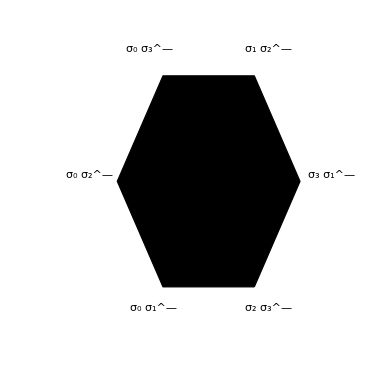

```mathematica
Graphics[{{AbsoluteThickness[1],EdgeForm[RGBColor[List[Rational[2060,255],Rational[163,255],Rational[8,85]]]],FaceForm[RGBColor[List[1,Rational[254,255],Rational[209,255]]]]
,
Polygon[{{1/2,-(1/2)Sqrt@3},{1,0},{1/2,1/2 Sqrt@3},{Rational[-1,2],1/2 Sqrt@3},List[-1,0],{Rational[-1,2],-(1/2)Sqrt@3}}]}
,
Inset["σ_2 σ_3^—",{1.3/2,-Sqrt[3]/2 1.2},BaseStyle->Directive[14]],
Inset["σ_3 σ_1^—",{1.35,0.05},BaseStyle->Directive[14]],
Inset["σ_1 σ_2^—",{1.3/2,1/2 Sqrt[3]1.25},BaseStyle->Directive[14]],
Inset["σ_0 σ_1^—",{-1.2/2,-Sqrt[3]/2 1.2},BaseStyle->Directive[14]],
Inset["σ_0 σ_2^—",{-1.3,0.05},BaseStyle->Directive[14]],
Inset["σ_0 σ_3^—",{-1.3/2,1/2 Sqrt[3]1.25},BaseStyle->Directive[14]]
}
,
Rule[Axes,False],Rule[AxesLabel,List[x,y]],Rule[ImageSize,{390,390}],Rule[PlotRange,List[{-1.6,1.6},List[-1.2,1.2]]],Rule[PlotRangePadding,Scaled[0.04]],Rule[Ticks,False]]
```

## Spacetime Paravector

### Definition

The spacetime can be represented as a paravector

x= x^μ σ_μ.

Sometimes we write

x= x^0 σ_0 + x,

where the bold symbols stand for standard three-dimensional vectors

```mathematica
(x = x^0 Subscript[σ, 0]+ x^1 Subscript[σ, 1]+x^2 Subscript[σ, 2]+x^3 Subscript[σ, 3])//MatrixForm
```

(x^0+x^3 | x^1-ⅈ x^2
x^1+ⅈ x^2 | x^0-x^3)

```mathematica
1/2 Tr[x.Subscript[σ, 1] ]
```

x^1

Similarly, the proper velocity is

u= u^μ σ_μ

```mathematica
(u=u^0 Subscript[σ, 0]+ u^1 Subscript[σ, 1]+u^2 Subscript[σ, 2]+u^3 Subscript[σ, 3])//MatrixForm
```

(u^0+u^3 | u^1-ⅈ u^2
u^1+ⅈ u^2 | u^0-u^3)

The contraction of paravectors is accomplished as

```mathematica
1/2 Tr[x.u^—]//Simplify
```

u^0 x^0-u^1 x^1-u^2 x^2-u^3 x^3

```mathematica
1/2 Tr[u.u^—]//Simplify
```

(u^0)^2-(u^1)^2-(u^2)^2-(u^3)^2

The spacetime position has 4 degrees of freedom but the proper velocity has only 3 because it must obey the shell-mass constrain

(u^0)^2-(u^1)^2-(u^2)^2-(u^3)^2=c^2

also written as

1/2 Tr(u.u^—)=c^2

or

(u^0)^2-u^2=c^2

### Lorentz Transformations for paravectors

The Lorentz Boost is defined as the square root of the proper velocity

B=√(u/c) ,

where we note that B is Hermitian.

A useful formula for the square root is

B= (u+  c σ_0)/(√(2 c ( c + u^0))) .

The active Lorentz Boost is carried out by double side multiplication

x→y= L x L^†.

Considering that the Boost is a Hermitian Lorentz operator we have

x→y=  B x B.

Note : The Lorentz transformation for biparavectors is different and will be treated later.

```mathematica
(BoostSL2C[ u^0:_,u^1:_,u^2:_,u^3:_]=Module[{},((u^0 Subscript[σ, 0]+u^1 Subscript[σ, 1]+u^2 Subscript[σ, 2]+u^3 Subscript[σ, 3] )+  c Subscript[σ, 0])/(√(2 c ( c + u^0)))])//MatrixForm
```

((c+u^0+u^3)/(√2 √(c (c+u^0))) | (u^1-ⅈ u^2)/(√2 √(c (c+u^0)))
(u^1+ⅈ u^2)/(√2 √(c (c+u^0))) | (c+u^0-u^3)/(√2 √(c (c+u^0))))

Recovering the proper velocity from the Boost to verify the formula (using the shell mass condition)

```mathematica
Simplify[c BoostSL2C[ u^0,u^1,u^2,u^3].BoostSL2C[ u^0,u^1,u^2,u^3]];
U== Simplify[%/.{(u^1)^2+(u^2)^2+(u^3)^2->(u^0)^2- c^2}]
```

U=={{u^0+u^3,u^1-ⅈ u^2},{u^1+ⅈ u^2,u^0-u^3}}

The boost operator along x^3 is

```mathematica
BoostSL2C[ u^0,0,0,u^3]//MatrixForm
```

((c+u^0+u^3)/(√2 √(c (c+u^0))) | 0
0 | (c+u^0-u^3)/(√2 √(c (c+u^0))))

The active boost of the coordinates is

```mathematica
y=Simplify[BoostSL2C[ u^0,0,0,u^3].x.BoostSL2C[ u^0,0,0,u^3]]
```

{{((c+u^0+u^3)^2 (x^0+x^3))/(2 c (c+u^0)),((c+u^0-u^3) (c+u^0+u^3) (x^1-ⅈ x^2))/(2 c (c+u^0))},{((c+u^0-u^3) (c+u^0+u^3) (x^1+ⅈ x^2))/(2 c (c+u^0)),((c+u^0-u^3)^2 (x^0-x^3))/(2 c (c+u^0))}}

The transformation of coordinates reads

```mathematica
MapThread[Equal,{{y^0,y^1,y^2,y^3},Simplify[Simplify[1/2 Tr[y.Subscript[σ, #]]&/@{0,1,2,3}]/.{(u^3)^2->(u^0)^2- c^2}]}]//TableForm
```

y^0==(u^0 x^0+u^3 x^3)/c
y^1==x^1
y^2==x^2
y^3==(u^3 x^0+u^0 x^3)/c

```mathematica
{(u^0 x^0+u^3 x^3)/c,(u^3 x^0+u^0 x^3)/c}//.{c->1,u^0-> √(c^2+(u^3)^2)}
```

{√(1+(u^3)^2) x^0+u^3 x^3,u^3 x^0+√(1+(u^3)^2) x^3}

#### Spacetime diagram

The spacetime grid for a given velocity boost u^3 (The gray grid represents the rest frame and the blue grid represents the boosted frame)

```mathematica
Manipulate[
Graphics[{
{Blue,{Line/@Table[{(u^0 x^0+u^3 x^3)/c,(u^3 x^0+u^0 x^3)/c}//.{c->1,u^0-> √(c^2+(u^3)^2)},{x^3,-1,1,0.2},{x^0,-1,1,0.2}]
,
Line/@Table[{(u^0 x^0+u^3 x^3)/c,(u^3 x^0+u^0 x^3)/c}//.{c->1,u^0-> √(c^2+(u^3)^2)},{x^0,-1,1,0.2},{x^3,-1,1,0.2}]}}
,
{Darker@Blue,Thick,{Line@Table[{(u^0 x^0+u^3 x^3)/c,(u^3 x^0+u^0 x^3)/c}//.{c->1,u^0-> √(c^2+(u^3)^2),x^3->0},{x^0,-1,1,0.2}]
,
Line@Table[{(u^0 x^0+u^3 x^3)/c,(u^3 x^0+u^0 x^3)/c}//.{c->1,u^0-> √(c^2+(u^3)^2),x^0->0},{x^3,-1,1,0.2}]}}
,
{Gray,{Line/@Table[{(u^0 x^0)/c,(u^0 x^3)/c}//.{c->1,u^0-> c},{x^3,-1,1,0.2},{x^0,-1,1,0.2}]
,
Line/@Table[{(u^0 x^0)/c,(u^0 x^3)/c}//.{c->1,u^0-> c},{x^0,-1,1,0.2},{x^3,-1,1,0.2}]}}
},Axes->True,AxesLabel->{"x^3","x^0"},PlotRange->{{-1,1},{-1,1}}]
,{u^3,0,1}]
```

#### Array of clocks

A drawing of an array of clocks where the clocks in the rest frame are synchronized

```mathematica
SpacetimeClock[t_,z_]:=Graphics[{ Circle[{z,0},0.5] , Arrow[{{z,0},{z+0.5Sin[t],0.5Cos[t]}}]}];

BoostedSpacetimeClock[u^3:_][x^0:_,x^3:_]:=SpacetimeClock[y^0,y^3]/.{y^0:> √(1+(u^3)^2) x^0+u^3 x^3,y^3:> u^3 x^0+√(1+(u^3)^2) x^3}
```

The clocks are synchronized in the rest frame

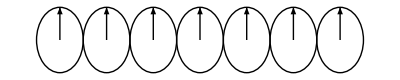

```mathematica
Show@@Table[
BoostedSpacetimeClock[u^3/.{u^3->0}][0,z],{z,-3,3,1}]
```

This system is actively boosted and now the clocks are not synchronized anymore as seen by the observer in the original rest frame

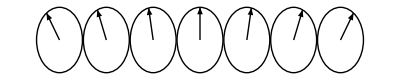

```mathematica
Show@@Table[
BoostedSpacetimeClock[u^3/.{u^3->0.2}][0,z],{z,-3,3,1}]
```

Given that the clocks are synchronized in the rest frame, what is the perception of an observer in a frame moving with velocity u^3?
The answer follows:

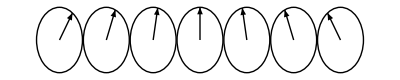

```mathematica
Show@@Table[
BoostedSpacetimeClock[u^3/.{u^3->-0.2}][0,z],{z,-3,3,1}]
```

#### Time dilation:

```mathematica
MapThread[Equal,{{y^0,x^1,x^2,0},Simplify[Simplify[1/2 Tr[y.Subscript[σ, #]]&/@{0,1,2,3}]/.{(u^3)^2->(u^0)^2- c^2}]}]
Refine[ Reduce[%,{y^0,x^3}], {x^3>0,x^0>0,y^0>0,c>0,u^0>0}];
First[%/.{(u^3)^2->(u^0)^2- c^2}]
```

{y^0==(u^0 x^0+u^3 x^3)/c,True,True,0==(u^3 x^0+u^0 x^3)/c}

y^0==(c x^0)/u^0

#### Length contraction:

```mathematica
MapThread[Equal,{{0,x^1,x^2,y^3},Simplify[Simplify[1/2 Tr[y.Subscript[σ, #]]&/@{0,1,2,3}]/.{(u^3)^2->(u^0)^2- c^2}]}]
Refine[ Reduce[%,{y^3,x^0}], {x^3>0,x^0>0,y^0>0,c>0,u^0>0}];
First[%/.{(u^3)^2->(u^0)^2- c^2}]
```

{0==(u^0 x^0+u^3 x^3)/c,True,True,y^3==(u^3 x^0+u^0 x^3)/c}

y^3==(c x^3)/u^0

## Paragradient

The paragradient is defined as

∂= σ_μ∂^μ =σ_0∂_0 - σ_k∂_k.

The Clifford conjugated paragradient is

OverBar[∂]= (σ̄)_μ∂^μ =σ_0∂_0 + σ_k∂_k.

```mathematica
paraGradient=(Subscript[σ, 0].D[#, x^0]- Subscript[σ, 1].D[#, x^1]-Subscript[σ, 2].D[#, x^2]-  Subscript[σ, 3].D[#, x^3])&
```

σ_0.∂_(x^0) #1-σ_1.∂_(x^1) #1-σ_2.∂_(x^2) #1-σ_3.∂_(x^3) #1&

```mathematica
paraGradientBar=(Subscript[σ, 0].D[#, x^0]+ Subscript[σ, 1].D[#, x^1]+Subscript[σ, 2].D[#, x^2]+  Subscript[σ, 3].D[#, x^3])&
```

σ_0.∂_(x^0) #1+σ_1.∂_(x^1) #1+σ_2.∂_(x^2) #1+σ_3.∂_(x^3) #1&

## Classical Electrodynamics

### Electromagnetic Field

The electromagnetic field as a biparavector is

F= F^(μ ν) ⟨σ_μ(σ̄)_μ⟩_V

which is expanded as

F=𝔼+ⅈ c 𝔹=σ_1 𝔼_1 + σ_2 𝔼_2 + σ_3 𝔼_3+ⅈ c( σ_1 𝔹_1+ σ_2 𝔹_2 + σ_3 𝔹_3)

The function that writes the electromagnetic paravector is

```mathematica
EMF["SL2C"][{Subscript[𝔼, 1]:_,Subscript[𝔼, 2]:_,Subscript[𝔼, 3]:_},{Subscript[𝔹, 1]:_,Subscript[𝔹, 2]:_,Subscript[𝔹, 3]:_}]= Subscript[σ, 1] Subscript[𝔼, 1] + Subscript[σ, 2] Subscript[𝔼, 2] + Subscript[σ, 3] Subscript[𝔼, 3]+ⅈ c( Subscript[σ, 1] Subscript[𝔹, 1]+ Subscript[σ, 2] Subscript[𝔹, 2] + Subscript[σ, 3] Subscript[𝔹, 3]);
```

For example we have

```mathematica
(F=EMF["SL2C"][{Subscript[𝔼, 1],Subscript[𝔼, 2],Subscript[𝔼, 3]},{Subscript[𝔹, 1],Subscript[𝔹, 2],Subscript[𝔹, 3]}]//Simplify)//MatrixForm
```

(ⅈ c 𝔹_3+𝔼_3 | c (ⅈ 𝔹_1+𝔹_2)+𝔼_1-ⅈ 𝔼_2
ⅈ c 𝔹_1-c 𝔹_2+𝔼_1+ⅈ 𝔼_2 | -ⅈ c 𝔹_3-𝔼_3)

```mathematica
EMFUpIndexComponents::usage="EMFUpIndexComponents[ X ], writes the biparavector electromagnetic field X as the components of the contravariant tensor components F^(μ ν) ";

EMFUpIndexComponents[EMF_]:=
If[Dimensions[EMF]=={2,2},
Simplify[
Table[
1/2Tr[ HermitianPart[ EMF.Inverse[(Subscript[σ, μ]).Subscript[σ, ν]^—]]]
,{μ,0,3},{ν,0,3}]/.Conjugate-> ForceConjugate
]
]
```

The (upper index) contravariant tensor components are

```mathematica
MatrixForm/@(F-> EMFUpIndexComponents[ F])//CompactFormat
```

(ⅈ c 𝔹_3+𝔼_3 | c (ⅈ 𝔹_1+𝔹_2)+𝔼_1-ⅈ 𝔼_2
ⅈ c 𝔹_1-c 𝔹_2+𝔼_1+ⅈ 𝔼_2 | -ⅈ c 𝔹_3-𝔼_3)→(0 | -𝔼_1 | -𝔼_2 | -𝔼_3
𝔼_1 | 0 | -c 𝔹_3 | c 𝔹_2
𝔼_2 | c 𝔹_3 | 0 | -c 𝔹_1
𝔼_3 | -c 𝔹_2 | c 𝔹_1 | 0)

### Vector potential

The electromagnetic field from the vector potential is

F=c⟨∂A^—⟩_V=c VectorPart[∂A^—]

Defining the paravector potential

```mathematica
A=A^0[x^0,x^1,x^2,x^3] Subscript[σ, 0]+A^1[x^0,x^1,x^2,x^3] Subscript[σ, 1]+A^2[x^0,x^1,x^2,x^3] Subscript[σ, 2]+A^3[x^0,x^1,x^2,x^3] Subscript[σ, 3];
```

The electromagnetic field is calculated as

```mathematica
ℱ=c VectorPart[∂A^—]//Simplify;
```

Calculating the upper tensor components

```mathematica
EMFUpIndexComponents[ ℱ ]//CompactFormat//MatrixForm
```

(0 | c (∂_1 A^0+∂_0 A^1) | c (∂_2 A^0+∂_0 A^2) | c (∂_3 A^0+∂_0 A^3)
-c (∂_1 A^0+∂_0 A^1) | 0 | c (∂_2 A^1-∂_1 A^2) | c (∂_3 A^1-∂_1 A^3)
-c (∂_2 A^0+∂_0 A^2) | c (-∂_2 A^1+∂_1 A^2) | 0 | c (∂_3 A^2-∂_2 A^3)
-c (∂_3 A^0+∂_0 A^3) | c (-∂_3 A^1+∂_1 A^3) | c (-∂_3 A^2+∂_2 A^3) | 0)

Comparing with the given contravariant electromagnetic tensor components

```mathematica
EMFUpIndexComponents[ F ]//MatrixForm
```

(0 | -𝔼_1 | -𝔼_2 | -𝔼_3
𝔼_1 | 0 | -c 𝔹_3 | c 𝔹_2
𝔼_2 | c 𝔹_3 | 0 | -c 𝔹_1
𝔼_3 | -c 𝔹_2 | c 𝔹_1 | 0)

### Energy Density and Poynting vector (Non covariant)

The energy density ℰ and Poynting S vector are obtained as

1/2 ε_0 c F F^† = ℰ c + S

with

ℰ = 1/2 ε_0( 𝔼^2 +c^2 𝔹^2)

S = 1/μ_0 𝔼 × 𝔹

Calculating the following expression

```mathematica
FF =Simplify[1/2 F.SuperDagger[(F)]/.Conjugate->ForceConjugate];
```

the energy density is

```mathematica
FullSimplify[1/2 Tr[ Subscript[ε, 0]  FF]]//MatrixForm//CompactFormat
```

1/2 (c^2 (𝔹_1^2+𝔹_2^2+𝔹_3^2)+𝔼_1^2+𝔼_2^2+𝔼_3^2) ε_0

and the Poynting vector is

```mathematica
Expand@Simplify[Simplify[VectorPart[Subscript[ε, 0] c FF]]/.{c^2-> 1/(Subscript[ε, 0] Subscript[μ, 0])}]//MatrixForm//CompactFormat
```

((𝔹_2 𝔼_1)/μ_0-(𝔹_1 𝔼_2)/μ_0 | (ⅈ 𝔹_3 𝔼_1)/μ_0+(𝔹_3 𝔼_2)/μ_0-(ⅈ 𝔹_1 𝔼_3)/μ_0-(𝔹_2 𝔼_3)/μ_0
-(ⅈ 𝔹_3 𝔼_1)/μ_0+(𝔹_3 𝔼_2)/μ_0+(ⅈ 𝔹_1 𝔼_3)/μ_0-(𝔹_2 𝔼_3)/μ_0 | -(𝔹_2 𝔼_1)/μ_0+(𝔹_1 𝔼_2)/μ_0)

### Determinant of the electromagnetic field as Lorentz invariant

The fact that 1/2 Tr[F^2] is Lorentz invariant implies the invariance of two quantities

```mathematica
FullSimplify[1/2 Tr@HermitianPart[F.F]/.Conjugate->ForceConjugate]//CompactFormat//MatrixForm
```

-c^2 (𝔹_1^2+𝔹_2^2+𝔹_3^2)+𝔼_1^2+𝔼_2^2+𝔼_3^2

```mathematica
FullSimplify[1/2 Tr@AntiHermitianPart[F.F]/.Conjugate->ForceConjugate]//CompactFormat//MatrixForm
```

2 ⅈ c (𝔹_1 𝔼_1+𝔹_2 𝔼_2+𝔹_3 𝔼_3)

Moreover

1/2 Tr[F^2] = -Det[F]

```mathematica
-RealPart@Det[F]/.Conjugate->ForceConjugate//Simplify//CompactFormat
```

-c^2 (𝔹_1^2+𝔹_2^2+𝔹_3^2)+𝔼_1^2+𝔼_2^2+𝔼_3^2

```mathematica
-ImaginaryPart@Det[F]/.Conjugate->ForceConjugate//Simplify//CompactFormat
```

2 ⅈ c (𝔹_1 𝔼_1+𝔹_2 𝔼_2+𝔹_3 𝔼_3)

### Maxwell Equations

The Maxwell equations are

OverBar[∂]F= cμ_0 j̄.

where the para-current is

j=c ρ + j.

The four standard Maxwell equations are

Gauss Law :

⟨OverBar[∂]F⟩_SH=ρ/ϵ_0

Ampere Maxwell Law :

⟨OverBar[∂]F⟩_VH=-cμ_0 j.

No magnetic monopoles:

⟨OverBar[∂]F⟩_SA=0

Faraday Maxwell:

⟨OverBar[∂]F⟩_VA=0

Note : The coefficient cμ_0 has units of impedance with value. For the vacuum we have

```mathematica
UnitSimplify[Quantity["SpeedOfLight"]*Quantity["MagneticConstant"]]//N
```

376.73 Ω

Quantum resistivity

```mathematica
2 Quantity["ElementaryCharge"]^2/Quantity["ReducedPlanckConstant"]
1/UnitSimplify[%]
```

2 e^2/ℏ

2054.12 Ω

Note : The presence of magnetic monopoles would require to  add a magnetic current as a triparavector, where the magnetic  charge would be a pseudoscalar that changes sign by a spatial reflections. Otherwise, electric charges are scalars that do not change under spatial reflections.

Homogeneous case:

∂^— F=0

Defining the electromagnetic field dependent on the spacetime.

```mathematica
F=EMF["SL2C"][{Subscript[𝔼, 1][x^0,x^1,x^2,x^3],Subscript[𝔼, 2][x^0,x^1,x^2,x^3],Subscript[𝔼, 3][x^0,x^1,x^2,x^3]},{Subscript[𝔹, 1][x^0,x^1,x^2,x^3],Subscript[𝔹, 2][x^0,x^1,x^2,x^3],Subscript[𝔹, 3][x^0,x^1,x^2,x^3]}]//Simplify;
```

The homogeneous Maxwell equations are

```mathematica
MaxwellEqs=∂^— (F)//Simplify;
```

#### Gauss Law

⟨∂^— F⟩_SH=0

∇∘𝔼 =0

```mathematica
Simplify[ -ScalarPart@HermitianPart[∂^— (F)]/.Conjugate-> ForceConjugate]//MatrixForm//CompactFormat
```

(-∂_1 𝔼_1-∂_2 𝔼_2-∂_3 𝔼_3 | 0
0 | -∂_1 𝔼_1-∂_2 𝔼_2-∂_3 𝔼_3)

#### Ampere Maxwell

⟨∂^— F⟩_HV=0

-c∇×𝔹+ (∂𝔼)/(∂x^0) =0

```mathematica
Simplify[ VectorPart@HermitianPart[∂^— (F)]/.Conjugate-> ForceConjugate]//MatrixForm//CompactFormat
```

(c ∂_2 𝔹_1-c ∂_1 𝔹_2+∂_0 𝔼_3 | ⅈ c ∂_3 𝔹_1+c ∂_3 𝔹_2-ⅈ c ∂_1 𝔹_3-c ∂_2 𝔹_3+∂_0 𝔼_1-ⅈ ∂_0 𝔼_2
-ⅈ c ∂_3 𝔹_1+c ∂_3 𝔹_2+ⅈ c ∂_1 𝔹_3-c ∂_2 𝔹_3+∂_0 𝔼_1+ⅈ ∂_0 𝔼_2 | -c ∂_2 𝔹_1+c ∂_1 𝔹_2-∂_0 𝔼_3)

Comparing with the standard formulation

```mathematica
c Curl[ {Subscript[𝔹, 1][x^0,x^1,x^2,x^3],Subscript[𝔹, 2][x^0,x^1,x^2,x^3],Subscript[𝔹, 3][x^0,x^1,x^2,x^3]},  {x^1,x^2,x^3}]-D[{Subscript[𝔼, 1][x^0,x^1,x^2,x^3],Subscript[𝔼, 2][x^0,x^1,x^2,x^3],Subscript[𝔼, 3][x^0,x^1,x^2,x^3]},x^0]//TableForm//CompactFormat
```

c (-∂_3 𝔹_2+∂_2 𝔹_3)-∂_0 𝔼_1
c (∂_3 𝔹_1-∂_1 𝔹_3)-∂_0 𝔼_2
c (-∂_2 𝔹_1+∂_1 𝔹_2)-∂_0 𝔼_3

#### No magnetic monopoles

⟨∂^— F⟩_AS=0

c∇∘𝔹=0

```mathematica
Simplify[ ScalarPart@AntiHermitianPart[∂^— (F)]/.Conjugate-> ForceConjugate]//MatrixForm//CompactFormat
```

(ⅈ c (∂_1 𝔹_1+∂_2 𝔹_2+∂_3 𝔹_3) | 0
0 | ⅈ c (∂_1 𝔹_1+∂_2 𝔹_2+∂_3 𝔹_3))

#### Maxwell Faraday

⟨∂^— F⟩_AV=0

∇×𝔼+ c(∂𝔹)/(∂x^0) =0

```mathematica
ExpandAll[ -I VectorPart@AntiHermitianPart[∂^— (F)]/.Conjugate-> ForceConjugate]//MatrixForm//CompactFormat
```

(c ∂_0 𝔹_3-∂_2 𝔼_1+∂_1 𝔼_2 | c ∂_0 𝔹_1-ⅈ c ∂_0 𝔹_2-ⅈ ∂_3 𝔼_1-∂_3 𝔼_2+ⅈ ∂_1 𝔼_3+∂_2 𝔼_3
c ∂_0 𝔹_1+ⅈ c ∂_0 𝔹_2+ⅈ ∂_3 𝔼_1-∂_3 𝔼_2-ⅈ ∂_1 𝔼_3+∂_2 𝔼_3 | -c ∂_0 𝔹_3+∂_2 𝔼_1-∂_1 𝔼_2)

Comparing with the standard formulation

```mathematica
Curl[ {Subscript[𝔼, 1][x^0,x^1,x^2,x^3],Subscript[𝔼, 2][x^0,x^1,x^2,x^3],Subscript[𝔼, 3][x^0,x^1,x^2,x^3]},  {x^1,x^2,x^3}]+c D[{Subscript[𝔹, 1][x^0,x^1,x^2,x^3],Subscript[𝔹, 2][x^0,x^1,x^2,x^3],Subscript[𝔹, 3][x^0,x^1,x^2,x^3]},x^0]//CompactFormat//TableForm
```

c ∂_0 𝔹_1-∂_3 𝔼_2+∂_2 𝔼_3
c ∂_0 𝔹_2+∂_3 𝔼_1-∂_1 𝔼_3
c ∂_0 𝔹_3-∂_2 𝔼_1+∂_1 𝔼_2

### Lorentz transformations for Biparavectors

The transformation law for the electromagnetic field is different compared with the transformation for paravectors

F → F'= L F L^—.

Let us remind that paravectors transform as

x → x'= L x L^†.

```mathematica
Simplify[BoostSL2C[ u^0,0,0,u^3].F.CliffordConjugationSL2C@BoostSL2C[ u^0,0,0,u^3]];
FullSimplify[EMFUpIndexComponents[%]/.{(u^3)^2->(u^0)^2- c^2}];
Simplify[%/.{(u^3)^2->(u^0)^2- c^2}]//CompactFormat//MatrixForm
```

```mathematica
({{0, -(c u^3 Subscript[𝔹, 2]+u^0 Subscript[𝔼, 1])/c, u^3 Subscript[𝔹, 1]-(u^0 Subscript[𝔼, 2])/c, -Subscript[𝔼, 3]}, {u^3 Subscript[𝔹, 2]+(u^0 Subscript[𝔼, 1])/c, 0, -c Subscript[𝔹, 3], u^0 Subscript[𝔹, 2]+(u^3 Subscript[𝔼, 1])/c}, {-u^3 Subscript[𝔹, 1]+(u^0 Subscript[𝔼, 2])/c, c Subscript[𝔹, 3], 0, -u^0 Subscript[𝔹, 1]+(u^3 Subscript[𝔼, 2])/c}, {Subscript[𝔼, 3], -(c u^0 Subscript[𝔹, 2]+u^3 Subscript[𝔼, 1])/c, u^0 Subscript[𝔹, 1]-(u^3 𝔼_2)/c, 0}})
```

The Lorentz transformation does not affect the parallel components of the electromagnetic field

```mathematica
{Tr[EMF["SL2C"][{0,0,Subscript[𝔼, 3]},{0,0,Subscript[𝔹, 3]}].Subscript[σ, 3]/2]-> 
ExpandAll@Tr[BoostSL2C[ u^0,0,0,u^3].EMF["SL2C"][{0,0,Subscript[𝔼, 3]},{0,0,Subscript[𝔹, 3]}].CliffordConjugationSL2C@BoostSL2C[ u^0,0,0,u^3].Subscript[σ, 3] /2]/.{(u^3)^2->(u^0)^2- c^2}//Simplify}
```

{ⅈ c 𝔹_3+𝔼_3→ⅈ c 𝔹_3+𝔼_3}

The following figure represents an electric field 𝔼_1 in a rest frame as a gray plane (x^0-x)^1  and the electromagnetic field (blue) as a result of a boost along u^3.  The boosted electromagnetic field is composed of an electric field 𝔼'_1 and an additional a magnetic field 𝔹'_2  spanning the plane (x^1-x)^3

```mathematica
BoostedE1[Subscript[𝔼, 1]:_,u^3:_,color_]:=
Graphics3D[{color,Opacity[0.8],Polygon[{{0,0,0},{0,u^3 Subscript[𝔼, 1],((2+2 (u^3)^2+2 √(1+(u^3)^2)) Subscript[𝔼, 1])/(2 (1+√(1+(u^3)^2)))},{1,u^3 Subscript[𝔼, 1],((2+2 (u^3)^2+2 √(1+(u^3)^2)) Subscript[𝔼, 1])/(2 (1+√(1+(u^3)^2)))},{1,0,0},{0,0,0}}]}
,Axes->True,AxesLabel->{"x^1","x^3","x^0"},
PlotRange->{{0,1},{0,1},{0,1.2}},
ViewPoint->{1.3, 2, 2.},Lighting->"Neutral"]
```

```mathematica
Show[
BoostedE1[0.8,0.,Gray],
BoostedE1[0.8,0.5,Blue]
]
```

-Graphics3D-

### Lorentz Force

The Lorentz force is calculated as

m ⅆ/ⅆτ u^μ = e/c F^μν u_ν = ⟨e/c F u ⟩_H

```mathematica
Simplify[1/c Subscript[⟨F.u⟩, "H"] /.Conjugate->ForceConjugate]//Simplify//CompactFormat//MatrixForm
```

((-c u^2 𝔹_1+c u^1 𝔹_2+u^1 𝔼_1+u^2 𝔼_2+u^0 𝔼_3+u^3 𝔼_3)/c | -ⅈ u^3 𝔹_1-u^3 𝔹_2+ⅈ u^1 𝔹_3+u^2 𝔹_3+(u^0 𝔼_1)/c-(ⅈ u^0 𝔼_2)/c
ⅈ u^3 𝔹_1-u^3 𝔹_2-ⅈ u^1 𝔹_3+u^2 𝔹_3+(u^0 𝔼_1)/c+(ⅈ u^0 𝔼_2)/c | (c u^2 𝔹_1-c u^1 𝔹_2+u^1 𝔼_1+u^2 𝔼_2-u^0 𝔼_3+u^3 𝔼_3)/c)

Taking components we recover the standard formulas

```mathematica
1/2 Tr[(1/c Subscript[⟨F.u⟩, "H"]).Subscript[σ, 0]]/.Conjugate->ForceConjugate//Simplify
```

(u^1 𝔼_1[x^0,x^1,x^2,x^3]+u^2 𝔼_2[x^0,x^1,x^2,x^3]+u^3 𝔼_3[x^0,x^1,x^2,x^3])/c

```mathematica
1/2 Tr[(1/c Subscript[⟨F.u⟩, "H"]).Subscript[σ, 1]]/.Conjugate->ForceConjugate//Simplify
```

-u^3 𝔹_2[x^0,x^1,x^2,x^3]+u^2 𝔹_3[x^0,x^1,x^2,x^3]+(u^0 𝔼_1[x^0,x^1,x^2,x^3])/c

```mathematica
1/2 Tr[(1/c Subscript[⟨F.u⟩, "H"]).Subscript[σ, 1]]/.Conjugate->ForceConjugate//Simplify
```

-u^3 𝔹_2[x^0,x^1,x^2,x^3]+u^2 𝔹_3[x^0,x^1,x^2,x^3]+(u^0 𝔼_1[x^0,x^1,x^2,x^3])/c

```mathematica
1/2 Tr[(1/c Subscript[⟨F.u⟩, "H"]).Subscript[σ, 1]]/.Conjugate->ForceConjugate//Simplify
```

-u^3 𝔹_2[x^0,x^1,x^2,x^3]+u^2 𝔹_3[x^0,x^1,x^2,x^3]+(u^0 𝔼_1[x^0,x^1,x^2,x^3])/c

## Spinorial Classical Dynamics

The proper velocity  u can be written in terms of the associated spinor Λ (also known as proper spinor or eigenspinor)

u = c Λ Λ^†.

The most general equation of motion for the spinor can be written in terms of a biparavector Ω

ⅆ/ⅆτ Λ = 1/2 Ω Λ ,

where we can identify Ω in terns of the electromagnetic field  F as

Ω = e/(m c)F ,

yielding the dynamical equation

ⅆ/ⅆτ Λ = e/(2m c)F Λ .

In general, the complete dynamics is determined by the coupled  equations:

ⅆ/ⅆτ Λ = e/(2m c)F Λ ,
					              ⅆ/ⅆτ x = c Λ Λ^†.

However, it is possible to show that for directed electromagnetic waves, these equations decouple and lead to the classical Volkov solutions.

### Charged particle in a constant electric field

Let us take the case of an electric field along the x direction

F=𝔼_0 σ_1

The integration of Eq (21) gives

Λ= e^((e 𝔼_0)/(2m c)σ_1 τ) Λ(0)

The initial the condition

Λ(0)=1

results in

```mathematica
ΛSol ={ Λ-> MatrixExp[   (e Subscript[𝔼, 0])/(2m c)  Subscript[σ, 1] τ]}//ExpToTrig
```

{Λ→{{Cosh[(e 𝔼_0 τ)/(2 c m)],Sinh[(e 𝔼_0 τ)/(2 c m)]},{Sinh[(e 𝔼_0 τ)/(2 c m)],Cosh[(e 𝔼_0 τ)/(2 c m)]}}}

The proper velocity is

u=Λ Λ^†= e^((e 𝔼_0)/(m c)σ_1 τ)

```mathematica
(uSol = {u->  Λ.Λ  /.ΛSol//ExpToTrig//Simplify});
```

For a particular initial condition, the spacetime trajectory can be integrated as

x=(m c)/(e 𝔼_0)  e^((e 𝔼_0)/(m c)σ_1 τ) σ_1

```mathematica
xSol={ X-> (m c)/(e Subscript[𝔼, 0])MatrixExp[   (e Subscript[𝔼, 0])/(2m c)  Subscript[σ, 1] τ].Subscript[σ, 1]}
```

{X→{{(c (-1/2 ⅇ^(-(e 𝔼_0 τ)/(2 c m))+1/2 ⅇ^((e 𝔼_0 τ)/(2 c m))) m)/(e 𝔼_0),(c (1/2 ⅇ^(-(e 𝔼_0 τ)/(2 c m))+1/2 ⅇ^((e 𝔼_0 τ)/(2 c m))) m)/(e 𝔼_0)},{(c (1/2 ⅇ^(-(e 𝔼_0 τ)/(2 c m))+1/2 ⅇ^((e 𝔼_0 τ)/(2 c m))) m)/(e 𝔼_0),(c (-1/2 ⅇ^(-(e 𝔼_0 τ)/(2 c m))+1/2 ⅇ^((e 𝔼_0 τ)/(2 c m))) m)/(e 𝔼_0)}}}

The spacetime trajectory parametrized by the proper time can be extracted as

```mathematica
ct->Tr[ X.Subscript[σ, 0]/.xSol]//ExpToTrig
```

ct→(2 c m Sinh[(e 𝔼_0 τ)/(2 c m)])/(e 𝔼_0)

```mathematica
X^1 -> Tr[ X.Subscript[σ, 1]/.xSol]//ExpToTrig
```

X^1→(2 c m Cosh[(e 𝔼_0 τ)/(2 c m)])/(e 𝔼_0)

```mathematica
X^2 -> Tr[ X.Subscript[σ, 2]/.xSol]//ExpToTrig
```

X^2→0

```mathematica
X^3 -> Tr[ X.Subscript[σ, 3]/.xSol]//ExpToTrig
```

X^3→0

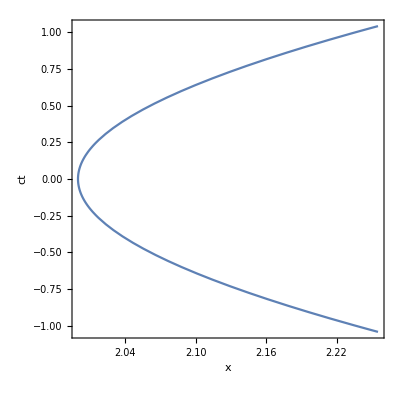

```mathematica
ParametricPlot[
Evaluate[ {Tr[ X.Subscript[σ, 1]/.xSol],Tr[ X.Subscript[σ, 0]/.xSol] }  /.{e->1, Subscript[𝔼, 0]->1,m->1,c->1}]
,{τ,-1,1},Frame->True,FrameLabel->{"x","ct"},AspectRatio->1,
BaseStyle->{FontSize->14}]
```

The determinant of the classical spinor is always 1

```mathematica
Det[ Λ/.ΛSol ]//Simplify
```

1

## The Dirac Equation

The Dirac equation can be written as

ⅈ c ℏ OverBar[∂] Ψ σ_3- c e Ā Ψ = m c^2 Ψ,

where the spinor Ψ is related to the standard Dirac spinor (Dirac basis) as

(ψ_1
ψ_2
ψ_3
ψ_4) ⟺(ψ_1+ψ_3 | -ψ_2^*+ψ_4^*
ψ_2+ψ_4 |    ψ_1^*-ψ_3^*).

In the Weyl column representation we have

(ψ_1
ψ_2
ψ_3
ψ_4) ⟺√2(ψ_3 | -ψ_2^*
ψ_4 |    ψ_1^*).

The current is given by

J =  Ψ Ψ^†,

which is similar to the formula for the proper velocity

u =  Λ Λ^†,

but in the case of the Dirac spinor we have

Det[Ψ]= e^ⅈβ,

where β is the Yvon-Takabayashi angle where β=0 for particles and β = -π  for  antiparticles.

The vector potential can be solved as

e Ā =(ⅈ  ℏ OverBar[∂] Ψ σ_3-m c Ψ)Ψ^-1.

```mathematica
DiracEquationSL2C[ψ_?MatrixQ,A_?MatrixQ,m_]:=Module[{K,ψc},
ψc= ConjugateTranspose[CliffordConjugationSL2C[ψ]];
K=ⅈ ℏ(Subscript[σ, 0].D[ψ, t]+c Subscript[σ, 1].D[ψ, x^1]+c Subscript[σ, 2].D[ψ, x^2]+ c Subscript[σ, 3].D[ψ, x^3]).Subscript[σ, 3] ;
 K-c A^—.ψ-m c^2  ψc
]
```

## References

Baylis, W.E., Electrodynamics : a modern geometric approach, Birkhauser, 1999

Baylis, W.E., Clifford (Geometric) Algebras : with applications to physics, mathematics, and engineering, Birkhauser, 1996

Baylis, W.E., Classical eigenspinors and the Dirac equation, Phys. Rev. A, 45, 4293, 1992